```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/hybrid_tail/math

```mathematica
Mpl=2.4 10^18;
M=10^16/Mpl;
ϕc=Sqrt[2]M;
μ2=10;
```

```mathematica
Π2=100;
μ1=Π2/(M^2 ϕc)
Λ=(5.4 10^15)/Mpl 10/Sqrt[Π2] M Sqrt[ϕc]
ψr=Sqrt[(Λ^4 Sqrt[Π2])/(48Sqrt[2 π^3])]
```

9.77504×10^8

7.19653×10^-7

8.42376×10^-14

### N = 2

```mathematica
ys={y1,y2};
pys={py1,py2};
wys={wy1,wy2};
ny=Length[ys];
ysN=Table[ys[[i]][NN],{i,ny}];
pysN=Table[pys[[i]][NN],{i,ny}];
```

```mathematica
V[x_,ys_]:=Λ^4((1-(ys.ys)/M^2)^2+2(x^2 ys.ys)/(M^2 ϕc^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2)
```

```mathematica
Vr[x_,yr_]=Λ^4((1-yr^2/M^2)^2+2(x^2 yr^2)/(M^2 ϕc^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
ηr[x_,yr_]=D[D[Vr[x,yr], yr], yr]/Vr[x,yr];
```

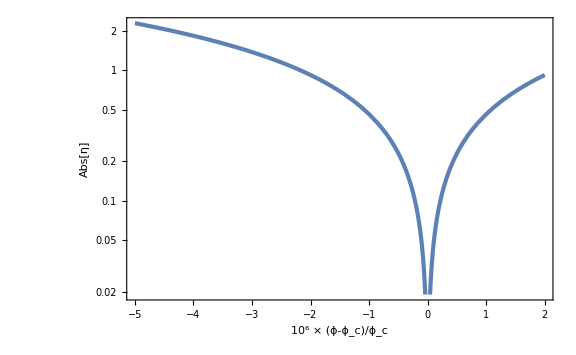

```mathematica
LogPlot[Abs[ηr[ϕc(1+dx 10^-6),0]],{dx,-5,2},GridLines->{None,{2}},FrameLabel->{Row[{"10^6 × ",(ϕ-Subscript[ϕ, "c"])/Subscript[ϕ, "c"]}],Abs[η]}]
```

```mathematica
H[x_,ys_,px_,pys_]:=Sqrt[(px^2/2+(pys.pys)/2+V[x,ys])/3]
```

```mathematica
EoMx={ⅆx[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](px[NN]/H[x[NN],ysN,px[NN],pysN] ⅆNN+H[x[NN],ysN,px[NN],pysN]/(2π)ⅆwx[NN]),
ⅆpx[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](-3px[NN]-D[V[x[NN],ysN], x[NN]]/H[x[NN],ysN,px[NN],pysN])ⅆNN};
EoMy=Flatten[Table[{ⅆysN[[i]]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](pysN[[i]]/H[x[NN],ysN,px[NN],pysN] ⅆNN+H[x[NN],ysN,px[NN],pysN]/(2π)ⅆwys[[i]][NN]),
ⅆpysN[[i]]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](-3pysN[[i]]-D[V[x[NN],ysN], ysN[[i]]]/H[x[NN],ysN,px[NN],pysN])ⅆNN},{i,ny}]];
```

```mathematica
IV=Flatten[{ϕc+15/μ1,0,Table[ψr,{i,ny}],Table[0,{i,ny}],0}];
```

```mathematica
prob=ItoProcess[Flatten[{EoMx,EoMy,ⅆNinf[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2]ⅆNN}],Flatten[{x[NN],px[NN],ysN,pysN,Ninf[NN]}],{Flatten[{x,px,ys,pys,Ninf}],IV},NN,Flatten[{wx\[Distributed]WienerProcess[],Table[wys[[i]]\[Distributed]WienerProcess[],{i,ny}]}]];
```

```mathematica
Nf=40;
sample=RandomFunction[prob,{0,Nf,0.01}];
```

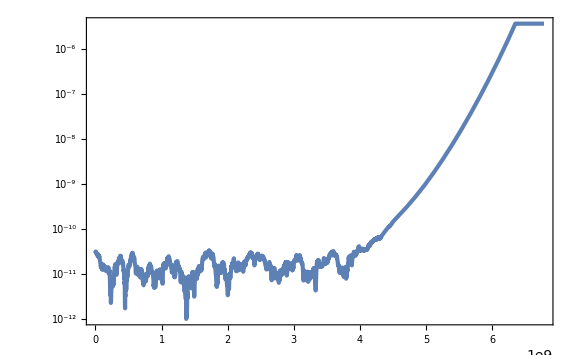

```mathematica
ParametricPlot[{(sample["PathFunction"][NN][[1]]-ϕc)/ϕc 10^6,Sqrt[Sum[(sample["PathFunction"][NN][[2+i]])^2,{i,ny}]]/M},{NN,0,Nf},ScalingFunctions->{"Linear","Log"}]
```

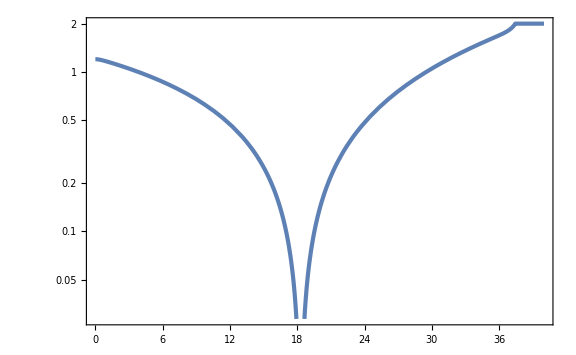

```mathematica
LogPlot[Abs[ηr[sample["PathFunction"][NN][[1]],Sqrt[Sum[(sample["PathFunction"][NN][[2+i]])^2,{i,ny}]]]],{NN,0,Nf}]//Quiet
```

```mathematica
deltaN=ItoProcess[Flatten[{EoMx,EoMy,ⅆNinf[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2]ⅆNN}],Ninf[NN],{Flatten[{x,px,ys,pys,Ninf}],IV},NN,Flatten[{wx\[Distributed]WienerProcess[],Table[wys[[i]]\[Distributed]WienerProcess[],{i,ny}]}]];
Nf=45;
dNsampling=ParallelTable[RandomFunction[deltaN,{0,Nf,0.01},10^3]["LastValues"],10^4]//Flatten;//AbsoluteTiming
```

{131212.,Null}

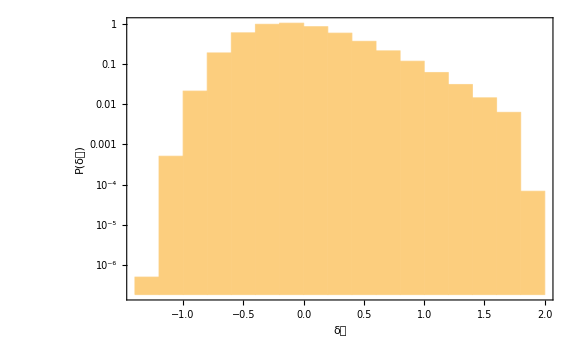

```mathematica
Histogram[dNsampling-Mean[dNsampling],Automatic,{"Log","PDF"},FrameLabel->{{P[δ𝒩],None},{δ𝒩,"waterfall = 2"}},PlotRange->Full]
```

```mathematica
Export["N=2_1e7.csv",dNsampling];
```

```mathematica
dNsamplingN2=Import["N=2_1e7.csv"]//Flatten;
```

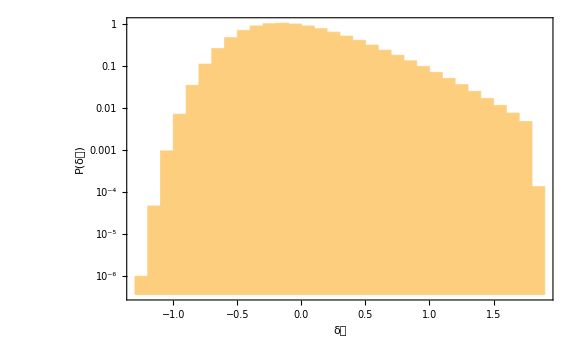

```mathematica
Histogram[dNsamplingN2-Mean[dNsamplingN2],30,{"Log","PDF"},FrameLabel->{{P[δ𝒩],None},{δ𝒩,"waterfall = 2"}},PlotRange->Full]
```

```mathematica
dNpartN2=Partition[dNsamplingN2,10^6];
```

```mathematica
binListN2=HistogramList[dNsamplingN2-Mean[dNsamplingN2],30,"PDF"][[1]];
```

```mathematica
HistoListN2=Table[HistogramList[dNpartN2[[i]]-Mean[dNpartN2[[i]]],{binListN2},"PDF"][[2]],{i,Length[dNpartN2]}]//Transpose;
```

```mathematica
JackHistoN2=Table[{(binListN2[[i]]+binListN2[[i+1]])/2,Mean[HistoListN2[[i]]]±StandardDeviation[HistoListN2[[i]]]/Sqrt[10]},{i,Length[binListN2]-1}];
JackHistoWOEN2=Table[{(binListN2[[i]]+binListN2[[i+1]])/2,Mean[HistoListN2[[i]]]},{i,Length[binListN2]-1}];
JackHistoErrN2=Table[StandardDeviation[HistoListN2[[i]]]/Sqrt[10],{i,Length[binListN2]-1}];
```

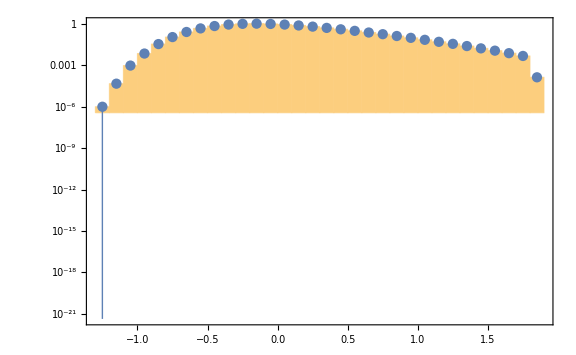

```mathematica
Show[Histogram[dNsamplingN2-Mean[dNsamplingN2],{binListN2},{"Log","PDF"},PlotRange->Full],ListLogPlot[JackHistoN2,Joined->False]]
```

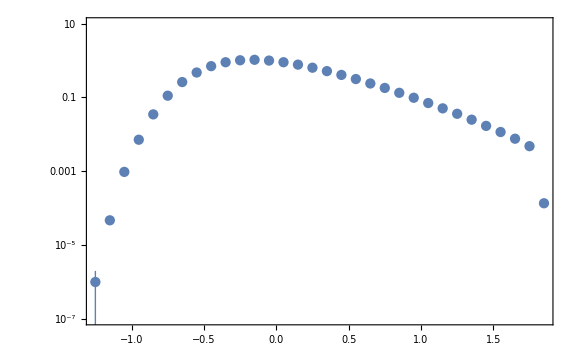

```mathematica
ListLogPlot[JackHistoN2,Joined->False,PlotRange->{10^-7,10}]
```

```mathematica
SUfitN2=NonlinearModelFit[JackHistoWOEN2,PDF[JohnsonDistribution["SU",γ,δ,μ,σ],x],{γ,δ,μ,σ},x(*,Weights->1/JackHistoErrN15^2*),MaxIterations->1000]
```

FittedModel[(1.26285 ⅇ^(-1/2 («1»)^2))/(√(0.235134+(1.2167+x)^2))]

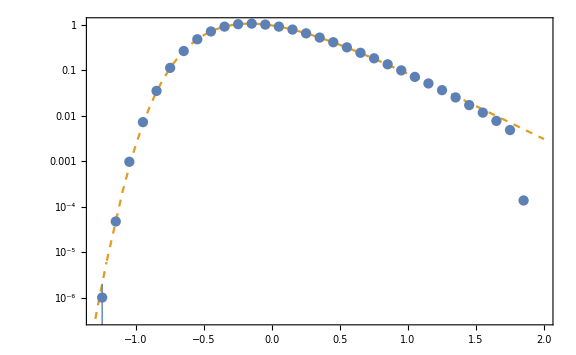

```mathematica
Show[LogPlot[Normal[SUfitN2],{x,-1.3,2},PlotStyle->{Color[2],Dashed}],ListLogPlot[JackHistoN2,Joined->False]]
```

### N = 15

```mathematica
ys={y1,y2,y3,y4,y5,y6,y7,y8,y9,y10,y11,y12,y13,y14,y15};
pys={py1,py2,py3,py4,py5,py6,py7,py8,py9,py10,py11,py12,py13,py14,py15};
wys={wy1,wy2,wy3,wy4,wy5,wy6,wy7,wy8,wy9,wy10,wy11,wy12,wy13,wy14,wy15};
ny=Length[ys];
ysN=Table[ys[[i]][NN],{i,ny}];
pysN=Table[pys[[i]][NN],{i,ny}];
```

```mathematica
V[x_,ys_]:=Λ^4((1-(ys.ys)/M^2)^2+2(x^2 ys.ys)/(M^2 ϕc^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2)
```

```mathematica
Vr[x_,yr_]=Λ^4((1-yr^2/M^2)^2+2(x^2 yr^2)/(M^2 ϕc^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
ηr[x_,yr_]=D[D[Vr[x,yr], yr], yr]/Vr[x,yr];
```

```mathematica
H[x_,ys_,px_,pys_]:=Sqrt[(px^2/2+(pys.pys)/2+V[x,ys])/3]
```

```mathematica
EoMx={ⅆx[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](px[NN]/H[x[NN],ysN,px[NN],pysN] ⅆNN+H[x[NN],ysN,px[NN],pysN]/(2π)ⅆwx[NN]),
ⅆpx[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](-3px[NN]-D[V[x[NN],ysN], x[NN]]/H[x[NN],ysN,px[NN],pysN])ⅆNN};
EoMy=Flatten[Table[{ⅆysN[[i]]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](pysN[[i]]/H[x[NN],ysN,px[NN],pysN] ⅆNN+H[x[NN],ysN,px[NN],pysN]/(2π)ⅆwys[[i]][NN]),
ⅆpysN[[i]]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](-3pysN[[i]]-D[V[x[NN],ysN], ysN[[i]]]/H[x[NN],ysN,px[NN],pysN])ⅆNN},{i,ny}]];
```

```mathematica
IV=Flatten[{ϕc+15/μ1,0,Table[ψr,{i,ny}],Table[0,{i,ny}],0}];
```

```mathematica
prob=ItoProcess[Flatten[{EoMx,EoMy,ⅆNinf[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2]ⅆNN}],Flatten[{x[NN],px[NN],ysN,pysN,Ninf[NN]}],{Flatten[{x,px,ys,pys,Ninf}],IV},NN,Flatten[{wx\[Distributed]WienerProcess[],Table[wys[[i]]\[Distributed]WienerProcess[],{i,ny}]}]];
```

```mathematica
Nf=40;
sample=RandomFunction[prob,{0,Nf,0.01}];
```

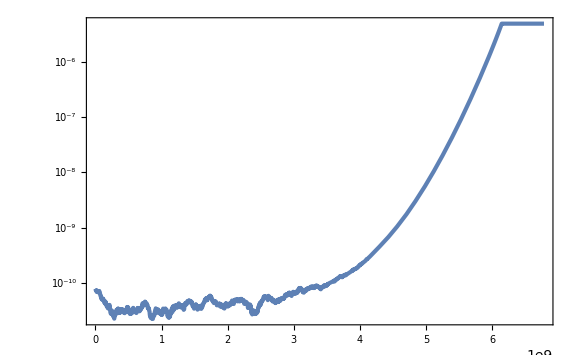

```mathematica
ParametricPlot[{(sample["PathFunction"][NN][[1]]-ϕc)/ϕc 10^6,Sqrt[Sum[(sample["PathFunction"][NN][[2+i]])^2,{i,ny}]]/M},{NN,0,Nf},ScalingFunctions->{"Linear","Log"}]
```

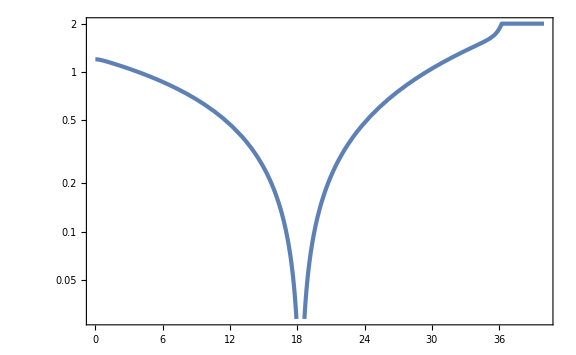

```mathematica
LogPlot[Abs[ηr[sample["PathFunction"][NN][[1]],Sqrt[Sum[(sample["PathFunction"][NN][[2+i]])^2,{i,ny}]]]],{NN,0,Nf}]//Quiet
```

```mathematica
deltaN=ItoProcess[Flatten[{EoMx,EoMy,ⅆNinf[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2]ⅆNN}],Ninf[NN],{Flatten[{x,px,ys,pys,Ninf}],IV},NN,Flatten[{wx\[Distributed]WienerProcess[],Table[wys[[i]]\[Distributed]WienerProcess[],{i,ny}]}]];
Nf=45;
dNsampling=ParallelTable[RandomFunction[deltaN,{0,Nf,0.01},10^3]["LastValues"],{i,10^2}]//Flatten;//AbsoluteTiming
```

{1106.12,Null}

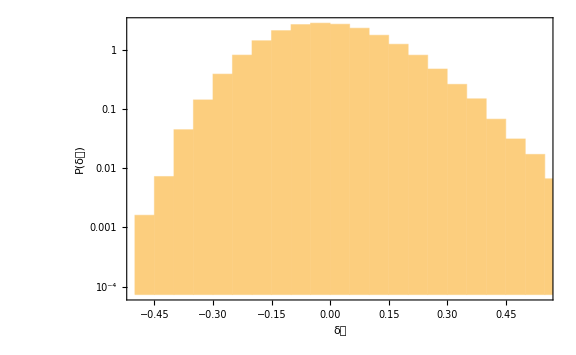

```mathematica
Histogram[dNsampling-Mean[dNsampling],Automatic,{"Log","PDF"},FrameLabel->{{P[δ𝒩],None},{δ𝒩,"waterfall = 15"}}]
```

```mathematica
dNsamplingN15=Import["N=15_1e7.csv"]//Flatten;
```

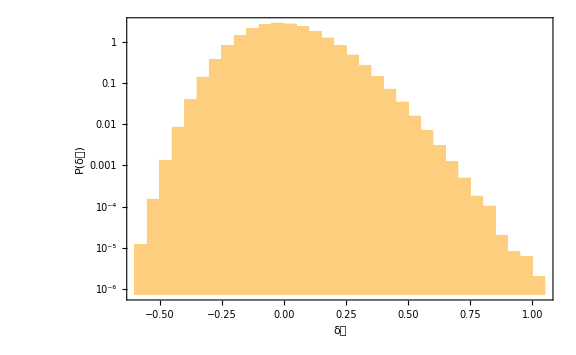

```mathematica
Histogram[dNsamplingN15-Mean[dNsamplingN15],30,{"Log","PDF"},FrameLabel->{{P[δ𝒩],None},{δ𝒩,"waterfall = 15"}},PlotRange->Full]
```

```mathematica
dNpartN15=Partition[dNsamplingN15,10^6];
```

```mathematica
binListN15=HistogramList[dNsamplingN15-Mean[dNsamplingN15],30,"PDF"][[1]];
```

```mathematica
binListN15
```

{-3/5,-11/20,-1/2,-9/20,-2/5,-7/20,-3/10,-1/4,-1/5,-3/20,-1/10,-1/20,0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1,21/20}

```mathematica
HistoListN15=Table[HistogramList[dNpartN15[[i]]-Mean[dNpartN15[[i]]],{binListN15},"PDF"][[2]],{i,Length[dNpartN15]}]//Transpose;
```

```mathematica
JackHistoN15=Table[{(binListN15[[i]]+binListN15[[i+1]])/2,Mean[HistoListN15[[i]]]±StandardDeviation[HistoListN15[[i]]]/Sqrt[10]},{i,Length[binListN15]-1}];
JackHistoWOEN15=Table[{(binListN15[[i]]+binListN15[[i+1]])/2,Mean[HistoListN15[[i]]]},{i,Length[binListN15]-1}];
JackHistoErrN15=Table[StandardDeviation[HistoListN15[[i]]]/Sqrt[10],{i,Length[binListN15]-1}];
```

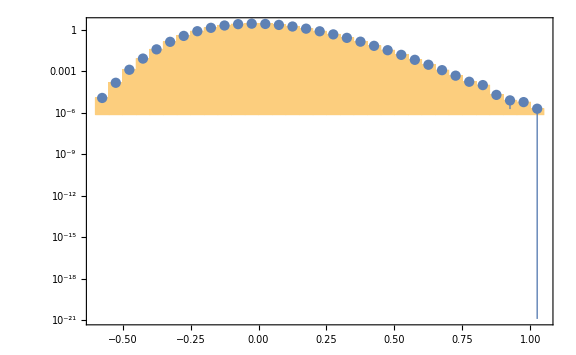

```mathematica
Show[Histogram[dNsamplingN15-Mean[dNsamplingN15],{binListN15},{"Log","PDF"},PlotRange->Full],ListLogPlot[JackHistoN15,Joined->False]]
```

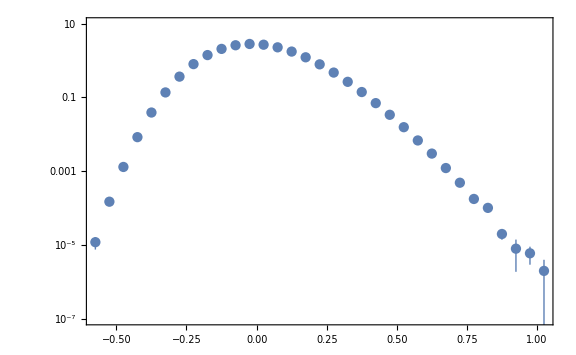

```mathematica
ListLogPlot[JackHistoN15,Joined->False,PlotRange->{10^-7,10}]
```

```mathematica
SUfitN15=NonlinearModelFit[JackHistoWOEN15,PDF[JohnsonDistribution["SU",γ,δ,μ,σ],x],{γ,δ,μ,σ},x(*,Weights->1/JackHistoErrN15^2*),MaxIterations->1000]
```

FittedModel[(3.15277 ⅇ^(-1/2 («1»)^2))/(√(0.37903+(0.94508+x)^2))]

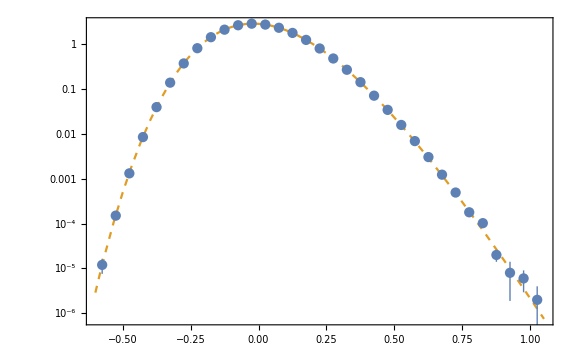

```mathematica
Show[LogPlot[Normal[SUfitN15],{x,-0.6,1.05},PlotStyle->{Color[2],Dashed}],ListLogPlot[JackHistoN15,Joined->False]]
```